# optical pumping and branching ratios

P. Huft

## constants and functions

```mathematica
e=1.6*^-19;a0=5*^-11;
ℏ=(6.602*^-34)/(2π);
c=2.998*^8;
d=2.992e a0 E1MatElemHF[{2,0,1/2},{1,0,1/2},0];
ϵ0=8.85*^-12;
E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(FF+J+1+i)√((2FF+1)(2J+1))SixJSymbol[{J,JJ,1},{FF,F,i}]ClebschGordan[{FF,mFF},{1,-q},{F,mF}];
```

## optical pumping of 87Rb into F=1,m=0

## required pump, repump power

We want enough pump and repump power to saturate all of the relevant transitions. π polarized D1 pump light on F=1 -> F’=1, effectively unpolarized repump on D2 line, F=2 -> F’=2 (we send the repump through all of the MOT beam paths).

```mathematica
i=3/2;(*nuclear spin*)
S=1/2;
E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(FF+J+1+i)√((2FF+1)(2J+1))SixJSymbol[{J,JJ,1},{FF,F,i}]ClebschGordan[{FF,mFF},{1,-q},{F,mF}];
```

The pump light needs to saturate 1,±1’->1’,±1’ on the D1 line, and the repump needs to saturate  2,m -> 2’,m’ for m in 1,2, on the D2 line.

```mathematica
γ5PThreeHalves=2π*6.0659*10^6;
γ5POneHalf=2π*5.7468*10^6;
ReducedMatElemFineD1=2.9923e a0;
ReducedMatElemFineD1=4.2275e a0;
```

```mathematica
"D1 pump saturation (μW/mm^2)"
ISatPump=(ϵ0 c ℏ^2 γ5POneHalf^2)/(4 (E1MatElemHF[{1,1,1/2},{1,1,1/2},0]ReducedMatElemFineD1)^2)
```

D1 pump saturation (μW/mm^2)

100.173

```mathematica
"D2 repump saturations(μW/mm^2), averaged over repump polarization"
Print[m=1,"->mF'"]
ISatRepump1=Sum[(ϵ0 c ℏ^2 γ5POneHalf^2)/(4 (E1MatElemHF[{2,m,1/2},{2,m+q,3/2},q]ReducedMatElemFineD1)^2),{q,{-1,0,1}}]/3
Print[m=2,"->mF'"]
ISatRepump2=Sum[(ϵ0 c ℏ^2 γ5POneHalf^2)/(4 (E1MatElemHF[{2,m,1/2},{2,m+q,3/2},q]ReducedMatElemFineD1)^2),{q,{-1,0}}]/2
```

D2 repump saturations(μW/mm^2), averaged over repump polarization

1->mF'

122.434

2->mF'

75.13

Now calculate how much power we need given our beam sizes

```mathematica
wPump=300*10^-6;(*1/ⅇ^2 intensity radius, m*)
wRepump=600*10^-6;
Ppump=π/2 wPump^2 ISatPump;
Prepump=π/2 wRepump^2 ISatRepump1;
"Pump power (μW)"
Ppump*10^6
"Repump power (μW)"
Prepump*10^6
"Repump power per MOT beam (μW)"
Prepump*10^6/6//N
```

Pump power (μW)

14.1617

Repump power (μW)

69.2348

Repump power per MOT beam (μW)

11.5391

Calculate the Rabi frequency to know how much power broadening to expect

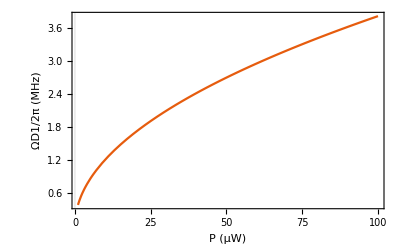

```mathematica
ϵ=√(s Isat/(2c ϵ0));
ΩD1=Abs[(ϵ E1MatElemHF[{1,1,1/2},{1,1,1/2},0]ReducedMatElemFineD1)/ℏ];
Plot[(ΩD1/(2π)/.s->(P*10^-6)/Ppump)/10^6,{P,1,100},FrameLabel->{"P (μW)","ΩD1/2π (MHz)"},PlotTheme->"Scientific"]
```

## depumping rate, no bias field, perfect polarization

Raman depumping example from Mark’s notes. Pump light on F=4-4 on the D1 line and repump on F=3-4 on the D2 line. Note that I get different values for bout and btotal compared to Mark, because my expression for the E1 matrix element hyperfine angular factor has the prefactor √(2F+1), which Mark omits. This is fine, because we are comparing decay from the same starting states F and this prefactor will cancel out.

This is estimate is probably very poor. For only 10 μW pumping power, the depump time is < 1 ms.

```mathematica
(*the angular factor in the dipole matrix element, up to the reduced matrix element in nLJ including the radial integral and orbital ang. mom. L, L'. We're only considering states with the same J.*)
i=3/2;
S=1/2;
E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(FF+J+1+i)√((2FF+1)(2J+1))SixJSymbol[{J,JJ,1},{FF,F,i}]ClebschGordan[{FF,mFF},{1,-q},{F,mF}];

(*Decay channels out of 5P1/2,F'=2,mF=0 that don't return to F=1,m=0*)
bout=2 E1MatElemHF[{2,0,1/2},{2,1,1/2},1]^2+2 E1MatElemHF[{2,0,1/2},{1,1,1/2},1]^2;
"bout"
bout
"btotal"(*there's some chance the Raman event scatters right back into the target state*)
btotal=bout+E1MatElemHF[{2,0,1/2},{1,0,1/2},0]^2
"fraction of Raman scattering out of |1,0>"
bout/btotal
```

bout

2/3

btotal

1

fraction of Raman scattering out of |1,0>

2/3

```mathematica
d=2.992e a0 E1MatElemHF[{2,0,1/2},{1,0,1/2},0];
γ=2π*5.746*^6;
Δ=2π*816.656*^6;(*energy splitting between 1'-2'*)
"Isat"
Isat=(ϵ0 c ℏ^2 γ^2)/(4 d^2)
Clear[P];
(*P=10*^-6;(*optical pumping power in Watts*)*)
w0=3*^-4;(*1/e^2 beam waist in m*)
s=(2 P)/(π w0^2)/Isat;
"ρee"
ρee=γ^2/(8 Δ^2)s;
"depumping rate out of |1,0> (s^-1)"
r=bout/btotal γ ρee
"depumping time out of|1,0> (s)"
1/r
```

Isat

49.9822

ρee

depumping rate out of |1,0> (s^-1)

2.10785×10^7 P

depumping time out of|1,0> (s)

(4.74417×10^-8)/P

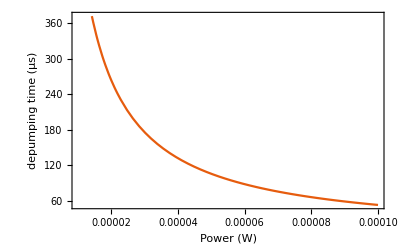

```mathematica
Plot[1/r 10^6,{P,10^-5,10^-4},PlotTheme->"Scientific",FrameLabel->{"Power (W)","depumping time (μs)"}]
```

## pump/repump angle for Rb Bell state

We didn’t use the results of this calculation in the end, but in any case it’s better to just simulate the master eq. evolution

Pumping sequence to target state 5S1/2 F=1,m=0. 
- D1 line OP on F=1-F=1: population in target state and 5S1/2 F=2 states.
- D2 line RP on F=2-F=2: moves population stuck in F=2 back into the bright states for the pump beam.
- D2 excitation on F=1-F=0: π pulse, then decay redistributes population to the 5S1/2 F=1 states.

Question: the OP and excitation are linear with angle θ=0 wrt the bias magnetic field. What is the optimal angle for the linearly polarized RP light in order to minimize the pumping sequence time?
	a. find the distribution of population in F=2 following the excitation and subsequent OP. The population in each of the F=2 states will weight the rates of rates that RP moves population back to F=1.
	b. find the rates that population is pumped from F=2,m to F=1 states, leaving the polarization angle undetermined. Sum to calculate the total rate of transfer from F=2 to F=1, then maximize in θ.
	
See my handwritten algebra in my turquoise Leuchturrm1917 notebook, pages 236,237, 2022.06.27-28.

population in 5S1/2 F=1 after decay from 5P3/2 F=0,m=0

{1/3,1/3,1/3}

ClebschGordan::phy: ThreeJSymbol[{2,-2},{1,0},{1,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,-2},{1,-1},{1,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,-2},{1,-1},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

Part::partw: Part 4 of {1/3,1/3,1/3} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

population in 5S1/2,F=2 states from pumping and subsequent decay

{1/10,1/4,3/10,1/4,1/10}

repump rate into F=1 states as a function of repump angle

ClebschGordan::phy: ThreeJSymbol[{2,-2},{1,-1},{1,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,-2},{1,-1},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,-2},{1,-1},{1,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

1/480 (47-27 Cos[2 θ])

angle [deg.] for fastest repump

{0.154167,{θ→1.5708}}

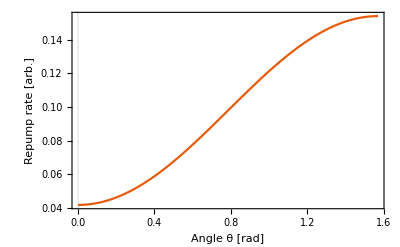

```mathematica
Clear[btotal]
i=3/2; (*Rb 87 nuclear spin*)
(*Wigner little d*)
d[j_,m1_,m2_,θ_]:=WignerD[{j,m2,m1},0,θ,0];
(*the angular factor in the dipole matrix element F'm'D(0,θ,0)Subscript[r, 0] D(0,θ,0)F,m. F'm' is the final state.*)
Cd[FF_,mm_,F_,m_,θ_]:=Sum[d[FF,mm,n,θ]d[F,m,n,θ]ClebschGordan[{F,n},{1,0},{FF,n}],{n,Range[-Min[F,FF],Min[F,FF]]}];
(*the angular factor in the electric dipole matrix element*)
E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(1+i+JJ+F)√(2F+1)SixJSymbol[{J,i,F},{FF,1,JJ}]ClebschGordan[{F,mF},{1,q},{FF,mFF}]
(*branching ratio for transitions from F,m to all F' states*)
bFmtoFF[{F_,m_,J_},{FF_,JJ_}]:=Sum[E1MatElemHF[{F,m,J},{FF,mm,JJ},q]^2,{q,{-1,0,1}},{mm,Range[-F,F]}];

(*starting with all of the population in 5P3/2,F=0,m=0, find the population in 5S1/2,F=2 states, after the starting population has decayed and been pumped on the D1 line.*)

Clear[ρ1vec]
F1g=1;(*F=1 in 5S1/2*)
F0e=0;(*F=0 in 5P3/2*)
Jg=1/2;(*J in 5S *)
Je=3/2;(*D2 line J in 5P.*)
F2g=2;(*F=2 in 5S1/2*)
F2e=2;(*F=2 in 5P1/2*)
F1e=2;(*F=1 in 5S1/2*)
ρ1vec=Table[E1MatElemHF[{F0e,0,Je},{F1g,mm,Jg},mm]^2,{mm,Range[-F1g,F1g]}];
"population in 5S1/2 F=1 after decay from 5P3/2 F=0,m=0"
ρ1vec/=Total[ρ1vec]
(*total branching to all 5S1/2 F levels from 5P1/2,F=1*)
btotal[m_]:=bFmtoFF[{F1e,m,Je},{F1g,Jg}]+bFmtoFF[{F1e,m,Je},{F2g,Jg}];
(*rate of pumping into 5S1/2 F=2 states*)
m2=Range[-F2g,F2g];
(*D1 pumping polarization*)
qpump=0;
(*pump rate from F=1,m to F'=1,m'=m-q*)
pumpRate[m_]:=E1MatElemHF[{F1e,m,Jg},{F1g,m-qpump,Jg},qpump]^2;
(*population in 5S1/2,F=2 states from pumping and subsequent decay*)
ρ2vec=
Table[Sum[ρ1vec[[m+F1g+1]]pumpRate[m] E1MatElemHF[{F1e,m,Jg},{F2g,m2[[idc]],Jg},m2[[idc]]-m]^2/btotal[m2[[idc]]],{m,Range[-F1e,F1e]}],{idc,Range[2*2+1]}];
"population in 5S1/2,F=2 states from pumping and subsequent decay"
ρ2vec/=Total[ρ2vec]
(*scattering rate to F=1 if we start with all of the population in F=2 states.*)
btotal[m_]:=bFmtoFF[{F2e,m,Je},{F1g,Jg}]+bFmtoFF[{F2e,m,Je},{F2g,Jg}];(*total branching ratio from state F=2,m. The ρ2 are the populations for the 5S1/2,F=2 states*)
"repump rate into F=1 states as a function of repump angle"
Rrp=Sum[Cd[2,m,2,n,θ]^2 bFmtoFF[{F2e,m,Je},{F1g,Jg}]/btotal[m] ρ2vec[[m+F2g+1]],{m,Range[-F2g,F2g]},{n,Range[-F1g,F1g]}]//FullSimplify
"angle [deg.] for fastest repump"
FindMaximum[Rrp,θ]
Plot[Rrp,{θ,0,π/2},PlotTheme->"Scientific",FrameLabel->{"Angle θ [rad]","Repump rate [arb.]"}]
```

What is the fraction of population left in F=2 from optical pumping? See my Obsidian notes.

```mathematica
g1=e1=1;  (*F=1 g and e levels*)
g2=e2=2;  (*F=2 g and e levels*)
q=0;
ρe1=Table[1/3 Sum[E1MatElemHF[{g1,mg1,1/2},{e1,me1,1/2},q]^2,{mg1,Range[-g1,g1]}],{me1,Range[-e1,e1]}];
"ρe1"
ρe1/=Total[ρe1](*normalize*)
"fractional population in g2 after decay from e1"
Sum[ρe1[[me1+2]] E1MatElemHF[{e1,me1,1/2},{g2,mg2,1/2},mg2-me1]^2,{me1,Range[-e1,e1]},{mg2,Range[-g2,g2]}]/Sum[ρe1[[me1+2]] E1MatElemHF[{e1,me1,1/2},{g1,mg1,1/2},mg1-me1]^2,{me1,Range[-e1,e1]},{mg1,Range[-g1,g1]}]
```

ClebschGordan::phy: ThreeJSymbol[{1,0},{1,0},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,0},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,0},{1,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

ρe1

{1/2,0,1/2}

fractional population in g2 after decay from e1

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,2},{2,-1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,3},{2,-2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,0},{1,-2},{2,2}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

5

```mathematica
Table[Sum[ρe1[[me1+2]] E1MatElemHF[{e1,me1,1/2},{g2,mg2,1/2},mg2-me1]^2,{me1,Range[-e1,e1]}],{mg2,Range[-g2,g2]}]
%//Total
```

ClebschGordan::phy: ThreeJSymbol[{1,0},{1,-2},{2,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,-3},{2,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,-2},{2,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

{1/8,1/16,1/24,1/16,1/8}

5/12

```mathematica
Table[Sum[ρe1[[me1+2]] E1MatElemHF[{e1,me1,1/2},{g1,mg1,1/2},mg1-me1]^2,{me1,Range[-e1,e1]}],{mg1,Range[-g1,g1]}]
%//Total
```

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,-2},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,2},{1,-1}] is not physical.

{1/48,1/24,1/48}

1/12

Simple minded sanity check to see if I believe that 83% of the decay ends up in F=2 as found above:

```mathematica
(3*3)/(3*2)(*3 states in F'=1 each have 3 decay channels to F=2 / 3 states in F='1 have 2 decay channels to F=1*)
```

3/2

This simple minded check says 60% of the population end up in F=2 states.

## equalizing D2 line excitation rates in Rb

Find the angle of linear polarization for which the Rabi frequency is equalized among transitions F=1,m to F=0,0 on the D2 line. See my algebra in Obsidian.

```mathematica
Table[ClebschGordan[{1,m},{1,-m},{0,0}]d[0,0,m,θ],{m,{-1,0,1}}]
```

{WignerD[{0,-1,0},0,θ,0]/(√3),-1/(√3),WignerD[{0,1,0},0,θ,0]/(√3)}

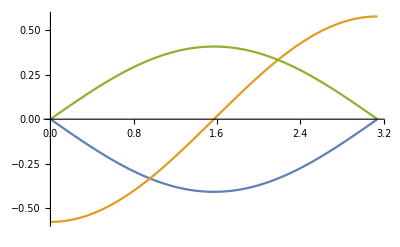

```mathematica
Plot[Evaluate[Table[ClebschGordan[{1,m},{1,-m},{0,0}]d[0,0,0,θ]d[1,0,m,θ],{m,{-1,0,1}}]],{θ,0.001,π}]
```

```mathematica
54.7*π/180
```

0.954695

```mathematica
WignerD[{0,-1,0},0,θ,0]
```

WignerD[{0,-1,0},0,θ,0]

```mathematica
d[0,0,1,θ]
```

WignerD[{0,1,0},0,θ,0]

```mathematica
Table[d[1,0,m,0],{m,{-1,0,1}}]
```

{0,1,0}

```mathematica
Table[{m,j},{{m,j},{Transpose@@{{Range[1,5],Range[1,5]}}}}]
```

Table::write: Tag List in {m,j} is Protected.

Table[{m,j},{{m,j},{{{1,1},{2,2},{3,3},{4,4},{5,5}}}}]

```mathematica
Transpose@@{{Range[1,5],Range[1,5]}}
```

{{1,1},{2,2},{3,3},{4,4},{5,5}}

## cesium depumping

Raman depumping example from Mark’s notes. Pump light on F=4-4 on the D1 line and repump on F=3-4 on the D2 line. Note that I get different values for bout and btotal compared to Mark, because my expression for the E1 matrix element hyperfine angular factor has the prefactor √(2F+1), which Mark omits. This is fine, because we are comparing decay from the same starting states F and this prefactor will cancel out.

```mathematica
(*the angular factor in the dipole matrix element, up to the reduced matrix element in nLJ including the radial integral and orbital ang. mom. L, L'*)
i=7/2;
S=1/2;(**)
E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(1+i+JJ+F)√(2F+1)SixJSymbol[{J,i,F},{FF,1,JJ}]ClebschGordan[{F,mF},{1,q},{FF,mFF}]

(*Decay channels out of 5P3/2,F=3,mF=0*)
b4out=2 E1MatElemHF[{3,0,1/2},{4,1,1/2},1]^2;
b3out=2 E1MatElemHF[{3,0,1/2},{3,1,1/2},1]^2;
"bout"
bout=b3out+b4out
"btotal"(*there's some chance the Raman event scatters right back into the target state*)
btotal=bout+E1MatElemHF[{3,0,1/2},{4,0,1/2},0]^2
"fraction of Raman scattering out of |4,0>"
bout/btotal
```

bout

1/3

btotal

1/2

fraction of Raman scattering out of |4,0>

2/3

## Clebsch-Gordan relations

The branching ratio is the square of the dipole matrix element for one decay channel over the sum of the squares of all of the decay channels. Mark seems to imply there is a shortcut for evaluating the sum. His expression uses F+ (I write Fp below) which is the lower F on a cycling transition.  I want to write a more general formula, to take care of decay from an upper state F’ < F, such as F’=0 to F=1 on the^87Rb D2 line.

```mathematica
i=3/2;
Jg=1/2;
Je=3/2;
Fp=1;

rkj[{JJ_,FF_,mFF_},{J_,F_,mF_}]:=(-1)^(1+i+J+FF)((2FF+1)/(2Fp+3))^(1/2)((SixJSymbol[{J,i,F},{FF,1,JJ}]ClebschGordan[{FF,mFF},{1,mF-mFF},{F,mF}])/(SixJSymbol[{Jg,i,Fp},{Fp+1,1,Je}]ClebschGordan[{Fp+1,Fp+1},{1,-1},{Fp,Fp}]))
```

```mathematica
statesk=Table[{Je,Fp+1,m},{m,Range[-(Fp+1),Fp+1]}]
statesj=Table[{Jg,Fp,m},{m,Range[-Fp,Fp]}]
```

{{3/2,2,-2},{3/2,2,-1},{3/2,2,0},{3/2,2,1},{3/2,2,2}}

{{1/2,1,-1},{1/2,1,0},{1/2,1,1}}

```mathematica
(*assert that Sum[Subscript[γ, j<-k]]=Subscript[γ, all<-k] for all k*)
Table[Sum[Quiet[rkj[statesk[[k]],statesj[[j]]]^2],{j,Length[statesj]}],{k,Length[statesk]}]
```

{1,1,1,1,1}

```mathematica
(*set q=mFF-mF which is always true*)
i=7/2;
E1MatElemHF[{J_,F_,mF_},{JJ_,FF_,mFF_},q_]:=(-1)^(1+i+JJ+F)√(2F+1)SixJSymbol[{J,i,F},{FF,1,JJ}]ClebschGordan[{F,mF},{1,q},{FF,mFF}];
bkj[{JJ_,FF_,mFF_},{J_,F_,mF_}]:=E1MatElemHF[{J,F,mF},{JJ,FF,mFF},mFF-mF]^2;btotal[{JJ_,FF_,mFF_}]:=Total[Flatten[Table[Table[E1MatElemHF[{Jg,Fg,mFg},{JJ,FF,mFF},mFF-mFg]^2,{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]
```

```mathematica
(*reproduce Cs depumping b=bout/btotal*)
Fglist={3,4};
Fe=3;
Je=1/2;
Jg=1/2;
statek={Je,Fe,0};
"ground states"
statesj=Flatten[Table[Table[{Jg,Fg,m},{m,Range[-Fg,Fg]}],{Fg,Fglist}],1]
"branch ratios out of 3',0"
allbranches=Table[bkj[statek,statesj[[j]]],{j,Range[Length[statesj]]}]
"btotal"
btot=Total[allbranches]
"btotal with function"
btotal[statek]
"bout"
bout=btot-bkj[statek,{Jg,4,0}]
"b=bout/btot"
bout/btot
```

ground states

{{1/2,3,-3},{1/2,3,-2},{1/2,3,-1},{1/2,3,0},{1/2,3,1},{1/2,3,2},{1/2,3,3},{1/2,4,-4},{1/2,4,-3},{1/2,4,-2},{1/2,4,-1},{1/2,4,0},{1/2,4,1},{1/2,4,2},{1/2,4,3},{1/2,4,4}}

branch ratios out of 3',0

ClebschGordan::phy: ThreeJSymbol[{3,-3},{1,3},{3,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3,-2},{1,2},{3,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3,2},{1,-2},{3,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

{0,0,1/16,0,1/16,0,0,0,0,0,5/48,1/6,5/48,0,0,0}

btotal

1/2

btotal with function

ClebschGordan::phy: ThreeJSymbol[{3,-3},{1,3},{3,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3,-2},{1,2},{3,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3,2},{1,-2},{3,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

1/2

bout

1/3

b=bout/btot

2/3

## how many photons scattered?

Atom with an isolated F=1 to F’=1 transition.

```mathematica
i=3/2;
E1MatElemHF[{J_,F_,mF_},{JJ_,FF_,mFF_},q_]:=(-1)^(1+i+JJ+F)√(2F+1)SixJSymbol[{J,i,F},{FF,1,JJ}]ClebschGordan[{F,mF},{1,q},{FF,mFF}];

(*fraction of photons scattered into the F=1,m=0 state given an excitation to F'=1,m'=1*)
η=E1MatElemHF[{1/2,1,0},{1/2,1,1},1]^2/(E1MatElemHF[{1/2,1,1},{1/2,1,1},0]^2+E1MatElemHF[{1/2,1,0},{1/2,1,1},1]^2)
(*initial population is Subscript[ρ, F=1,m]=1/3*)
ρF1m=1/3;
"mean photons scattered"
photons=1/(2η ρF1m)
```

1/2

mean photons scattered

3